# MATH7501 Practical 6 (Week 7), Semester 1-2021

## Topic: Sequences, Limits and Series

Author:  Aminath Shausan
Date: 16-04-2021

# Pre-Tutorial Activity

Students must have familiarised themselves with unit 5 contents  of the reading materials for MATH7501

# Resources

The Bisection Method (https://en.wikipedia.org/wiki/Bisection_method)

Mathematica Tutorial 23 - The bisection method for solving an equation by Dr Sam Hambelton

# Bisection Methodhe

The bisection method is a used to find an approximate solution to the equation f(x) = 0, for f continuous and defined in the interval [a , b] with f(a) and f(b) having opposite signs.  The method concerns of repeatedly dividing  the interval [a, b] into half then selecting the subinterval in which the function, f, changes sign, and therefore must contain a root by the Intermediate Value Theorem. The method is relatively slow compared to other root finding methods such as the Newton's method. However, the method is robust to errors as convergence is guaranteed. 

The bisection[ ] program below, which is described here, provides an elegant function to apply bisection method to approximate solution to a real valued function.   The program outputs an interval which approximates the solution, provided that the condition f(a)f(b) < 0 is met.

```mathematica
biSection[func_,{a_,b_},eps_?Positive]/;func[a]func[b]<0:=Module[{c,d,e},
{c,d}=If[func[a]>0,{b,a},{a,b}];
   While[Abs[d-c]>eps,  (* eps is the tolerance level*)
     With[{e=(c+d)/2},   (*this divides the interval [c,d] into half *)
       If[func[e]<0,c=e,d=e]
   ]
 ];
{c,d}   (* this is the interval containing the approximate solution*)
]
```

To run the program you will need to input

func:- an expression for the function in pure form (ie. you don’t need to define the function)

{a, b}:- the end points of the initial interval. You can either guess this or plot the function to decide this interval

eps:- the  tolerance level. The function ?Positive returns true if eps is positive.

To illustrate the use of the bisection function, let f(x)  = x^3 - x -2 and find an approximate solution in the interval [1,2], with eps = 0.5*10^-15.

```mathematica
biSection[#^3- #-2&,{1,2`20},.5*10^-15]
```

{1.5213797068045673555,1.5213797068045677996}

Example 1: Let f(x) = sinh(x-3) + x^3 -x^4+15. 
 Implement the bisection method on the interval [-1,3] .

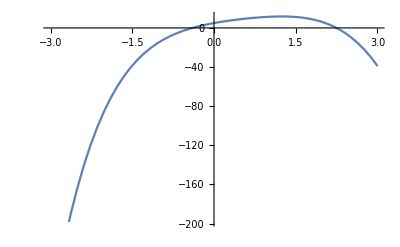

```mathematica
(* Lets first plot the function *)
Plot[Sinh[x-3]+x^3-x^4 +15, {x,-3, 3}]
```

We can see two roots in the interval [-1, 3]. Lets approximate the root in the interval [-1, 1] using the function bisection[ ].

```mathematica
biSection[Sinh[#-3]+#^3-#^4 +15&,{-1,1`20},.5*10^-15]
```

{-0.39649937993272743597,-0.39649937993272699188}

The approximate solution to f(x) = 0 in the interval [-1, 1] is -0.39649937993  us to 11 decimal places. You can find the second solution using a similar procedure. Try it by yourself

Example 2: Use Bisection method to find the intersection of  y = x and y = 1 - x^(2/5) .

```mathematica
(* First plot the two functions *)
```

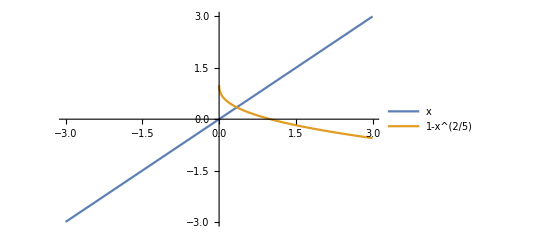

```mathematica
Plot[{x, 1-x^(2/5)}, {x,-3, 3}, PlotLegends->"Expressions"]
```

```mathematica
(*There seems to be a root between 0 and 1, so lets use the bisectio[] function to approximate theis *)
```

```mathematica
biSection[# -1+#^2/5&,{0,1`20},.5*10^-15]
```

{0.85410196624968426349,0.85410196624968470758}